```mathematica
SetOptions[SelectedNotebook[],PrintPrecision->16]
```

```mathematica
First example
```

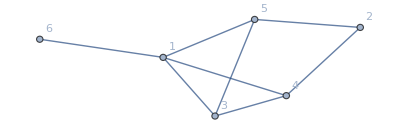

```mathematica
G=Graph[{1<->3,1<->4,1<->5,1<->6,2<->5,2<->4,3<->5,3<->4},VertexLabels->"Name"]
```

```mathematica
pp=0.347414311487909;
```

```mathematica
CIMult@PauliActionCC[G,4,Exact[1-2p,p,0,p],False]/.{p->pp}
CIMult@PauliActionCC[G,4,Exact[1-2p,p,0,p],True]/.{p->pp}
First[CIMult@PauliActionCC[G,4,Numeric[{1-2*pp,pp,0,pp}],True]]
```

-0.396753

group PermutationGroup[{Cycles[{{3,4}}]}]

Nested symmetry group or multiple hairs per orbit detected. CanonicalImage=nauty.

-0.396753

group PermutationGroup[{Cycles[{{3,4}}]}]

Nested symmetry group or multiple hairs per orbit detected. CanonicalImage=nauty.

-0.396753

```mathematica
(* cI from matlab (computed with graphstate code and directly): -0.405218214302711 *)
```

```mathematica
CIMult@PauliActionCC[G,5,Exact[1-2p,p,0,p],False]/.{p->pp}
CIMult@PauliActionCC[G,5,Exact[1-2p,p,0,p],True]/.{p->pp}
First[CIMult@PauliActionCC[G,5,Numeric[{1-2*pp,pp,0,pp}],True]]
```

-0.184517

group PermutationGroup[{Cycles[{{3,4}}]}]

Nested symmetry group or multiple hairs per orbit detected. CanonicalImage=nauty.

-0.184517

group PermutationGroup[{Cycles[{{3,4}}]}]

Nested symmetry group or multiple hairs per orbit detected. CanonicalImage=nauty.

-0.184517

```mathematica
(*cI(matlab) = -0.173150882079536 *)
```

```mathematica
CIMult@PauliActionCC[G,5,Exact[p],False]/.{p->pp}
CIMult@PauliActionCC[G,5,Exact[p],True]/.{p->pp}
First[CIMult@PauliActionCC[G,5,Numeric[{1-pp,pp/3,pp/3,pp/3}],True]]
```

-0.134993

group PermutationGroup[{Cycles[{{3,4}}]}]

Nested symmetry group or multiple hairs per orbit detected. CanonicalImage=nauty.

-0.134993

group PermutationGroup[{Cycles[{{3,4}}]}]

Nested symmetry group or multiple hairs per orbit detected. CanonicalImage=nauty.

-0.134993

```mathematica
(*cI(matlab) = -0.121318278216666 *)
```

```mathematica
CIMult@PauliActionCC[G,4,Exact[p],False]/.{p->pp}
CIMult@PauliActionCC[G,4,Exact[p],True]/.{p->pp}
First[CIMult@PauliActionCC[G,4,Numeric[{1-pp,pp/3,pp/3,pp/3}],True]]
```

-0.290243

group PermutationGroup[{Cycles[{{3,4}}]}]

Nested symmetry group or multiple hairs per orbit detected. CanonicalImage=nauty.

-0.290243

group PermutationGroup[{Cycles[{{3,4}}]}]

Nested symmetry group or multiple hairs per orbit detected. CanonicalImage=nauty.

-0.290243

```mathematica
(*ci(matlab) = -0.292517018307745 *)
```

```mathematica
q={0.292621706658177, 0.125557683029489, 0.226499729359284, 0.355320880953051};
```

```mathematica
CIMult@PauliActionCC[G,4,Exact[p0,p1,p2,p3],False]/.{p0->0.292621706658177,p1->0.125557683029489,p2->0.226499729359284,p3->0.355320880953051}
CIMult@PauliActionCC[G,4,Exact[p0,p1,p2,p3],True]/.{p0->0.292621706658177,p1->0.125557683029489,p2->0.226499729359284,p3->0.355320880953051}
First[CIMult@PauliActionCC[G,4,Numeric[q],True]]
```

-0.475937

group PermutationGroup[{Cycles[{{3,4}}]}]

Nested symmetry group or multiple hairs per orbit detected. CanonicalImage=nauty.

-0.475937

group PermutationGroup[{Cycles[{{3,4}}]}]

Nested symmetry group or multiple hairs per orbit detected. CanonicalImage=nauty.

-0.475937

```mathematica
(* cI(matlab) = -0.476552237250470 *)
```

Second example

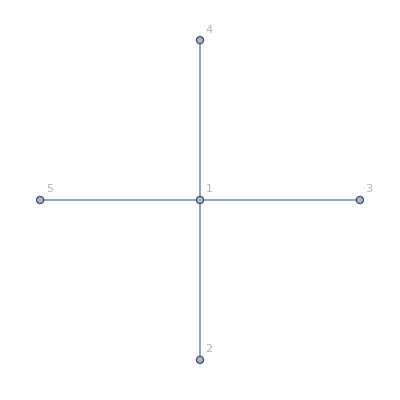

```mathematica
G = StarGraph[5,VertexLabels->"Name"]
```

```mathematica
pp=0.1135;
```

```mathematica
CIMult@PauliActionCC[G,3,Exact[1-2p,p,0,p],False]/.{p->pp}
CIMult@PauliActionCC[G,3,Exact[1-2p,p,0,p],True]/.{p->pp}
First[CIMult@PauliActionCC[G,3,Numeric[{1-2*pp,pp,0,pp}],True]]
```

-0.000668048

group PermutationGroup[{Cycles[{{2,3}}]}]

Product symmetry group detected. CanonicalImage=trivial.

-0.000668048

group PermutationGroup[{Cycles[{{2,3}}]}]

Product symmetry group detected. CanonicalImage=trivial.

-0.000668048

```mathematica
(*cI(matlab) = -6.680477911274648e-04 *)
```

```mathematica
CIMult@PauliActionCC[G,4,Exact[1-2p,p,0,p],False]/.{p->pp}
ci2=CIMult@PauliActionCC[G,4,Exact[1-2p,p,0,p],True]/.{p->pp}
ci3=First[CIMult@PauliActionCC[G,4,Numeric[{1-2*pp,pp,0,pp}],True]]
```

-0.00055459

group PermutationGroup[{Cycles[{{3,4}}],Cycles[{{2,3}}]}]

Product symmetry group detected. CanonicalImage=trivial.

-0.00055459

group PermutationGroup[{Cycles[{{3,4}}],Cycles[{{2,3}}]}]

Product symmetry group detected. CanonicalImage=trivial.

-0.00055459

```mathematica
Abs[ci2-ci3]
```

5.85837×10^-13

```mathematica
(*cI(matlab) = -5.545897656930032e-04 *)
```

```mathematica
CIMult@PauliActionCC[G,3,Exact[p],False]/.{p->pp}
ci2=CIMult@PauliActionCC[G,3,Exact[p],True]/.{p->pp}
ci3=First[CIMult@PauliActionCC[G,3,Numeric[{1-pp,pp/3,pp/3,pp/3}],True]]
```

0.10045

group PermutationGroup[{Cycles[{{2,3}}]}]

Product symmetry group detected. CanonicalImage=trivial.

0.10045

group PermutationGroup[{Cycles[{{2,3}}]}]

Product symmetry group detected. CanonicalImage=trivial.

0.10045

```mathematica
Abs[ci2-ci3]
```

3.92071×10^-12

```mathematica
(*cI(matlab) = 0.100449941657556 *)
```

```mathematica
CIMult@PauliActionCC[G,4,Exact[p],False]/.{p->pp}
ci2=CIMult@PauliActionCC[G,4,Exact[p],True]/.{p->pp}
ci3=First[CIMult@PauliActionCC[G,4,Numeric[{1-pp,pp/3,pp/3,pp/3}],True]]
```

0.0627167

group PermutationGroup[{Cycles[{{3,4}}],Cycles[{{2,3}}]}]

Product symmetry group detected. CanonicalImage=trivial.

0.0627167

group PermutationGroup[{Cycles[{{3,4}}],Cycles[{{2,3}}]}]

Product symmetry group detected. CanonicalImage=trivial.

0.0627167

```mathematica
(*cI(matlab) = 0.062716711372876 *)
```

```mathematica
Abs[ci2-ci3]
```

2.39303×10^-12

Third example (kSys is too big for direct computation in matlab, so only checking against matlab pauli_action code)

```mathematica
adjG={{0, 0, 0, 1, 1, 1, 1, 1, 0, 1}, {0, 0, 0, 1, 1, 1, 1, 1, 0, 0}, {0, 0, 0, 1, 0, 1, 1, 0, 0, 0}, {1, 1, 1, 0, 1, 1, 1, 0, 0, 0}, {1, 1, 0, 1, 0, 1, 0, 0, 1, 0}, {1, 1, 1, 1, 1, 0, 1, 0, 0, 0}, {1, 1, 1, 1, 0, 1, 0, 0, 0, 1}, {1, 1, 0, 0, 0, 0, 0, 0, 1, 1}, {0, 0, 0, 0, 1, 0, 0, 1, 0, 0}, {1, 0, 0, 0, 0, 0, 1, 1, 0, 0}};
```

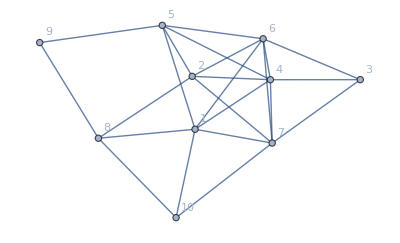

```mathematica
G=AdjacencyGraph[adjG,VertexLabels->"Name"]
```

```mathematica
GroupForGraph[G,#]&/@Range[6,9]
```

{PermutationGroup[{Cycles[{{4,6}}]}],PermutationGroup[{Cycles[{{4,6}}]}],PermutationGroup[{Cycles[{{4,6}}]}],PermutationGroup[{Cycles[{{4,6}}]}]}

```mathematica
pp=0.15;
```

```mathematica
CIMult@PauliActionCC[G,6,Exact[p],False]/.{p->pp}
ci2=CIMult@PauliActionCC[G,6,Exact[p],True]/.{p->pp}
ci3=First[CIMult@PauliActionCC[G,6,Numeric[{1-pp,pp/3,pp/3,pp/3}],True]]
```

0.116172

group PermutationGroup[{Cycles[{{4,6}}]}]

Nested symmetry group or multiple hairs per orbit detected. CanonicalImage=nauty.

0.116172

group PermutationGroup[{Cycles[{{4,6}}]}]

Nested symmetry group or multiple hairs per orbit detected. CanonicalImage=nauty.

0.116172

```mathematica
Abs[ci2-ci3]
```

8.77309×10^-12

```mathematica
(* cI(matlab) = 0.116171716565039 *)
```

```mathematica
CIMult@PauliActionCC[G,9,Exact[p],False]/.{p->pp}
ci2=CIMult@PauliActionCC[G,9,Exact[p],True]/.{p->pp}
ci3=First[CIMult@PauliActionCC[G,9,Numeric[{1-pp,pp/3,pp/3,pp/3}],True]]
```

0.0289599

group PermutationGroup[{Cycles[{{4,6}}]}]

Product symmetry group detected. CanonicalImage=trivial.

0.0289599

group PermutationGroup[{Cycles[{{4,6}}]}]

Product symmetry group detected. CanonicalImage=trivial.

0.0289599

```mathematica
Abs[ci2-ci3]
```

1.79902×10^-12

```mathematica
(* cI(matlab) = 0.028959917294108 *)
```

```mathematica
CIMult@PauliActionCC[G,7,Exact[1-2p,p,0,p],False]/.{p->pp}
ci2=CIMult@PauliActionCC[G,7,Exact[1-2p,p,0,p],True]/.{p->pp}
ci3=First[CIMult@PauliActionCC[G,7,Numeric[{1-2*pp,pp,0,pp}],True]]
```

-0.128924

group PermutationGroup[{Cycles[{{4,6}}]}]

Product symmetry group detected. CanonicalImage=trivial.

-0.128924

group PermutationGroup[{Cycles[{{4,6}}]}]

Product symmetry group detected. CanonicalImage=trivial.

-0.128924

```mathematica
(* cI(matlab) = -0.128923828530256 *)
```

```mathematica
CIMult@PauliActionCC[G,8,Exact[1-2p,p,0,p],False]/.{p->pp}
ci2=CIMult@PauliActionCC[G,8,Exact[1-2p,p,0,p],True]/.{p->pp}
ci3=First[CIMult@PauliActionCC[G,8,Numeric[{1-2*pp,pp,0,pp}],True]]
```

-0.0893189

group PermutationGroup[{Cycles[{{4,6}}]}]

Product symmetry group detected. CanonicalImage=trivial.

-0.0893189

group PermutationGroup[{Cycles[{{4,6}}]}]

Product symmetry group detected. CanonicalImage=trivial.

-0.0893189

```mathematica
(* cI(matlab) = -0.089318916244704 *)
```

```mathematica
q = {0.238549528757776, 0.317414265755037, 0.380042662093764, 0.063993543393423};
```

```mathematica
First[CIMult@PauliActionCC[G,6,Numeric[q],True]]
```

group PermutationGroup[{Cycles[{{4,6}}]}]

Nested symmetry group or multiple hairs per orbit detected. CanonicalImage=nauty.

-0.576043

```mathematica
(* cI(matlab) = -0.576042985962965 *)
```

```mathematica
Abs[-0.5760429865281653 - (-0.576042985962965)]
```

5.652×10^-10